```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\HILL\Documents\GitHub\thesis\figures\oscillator

```mathematica
v={6,7,8,10,11};
g={2,5.2,6.9,7.5,7.9};
```

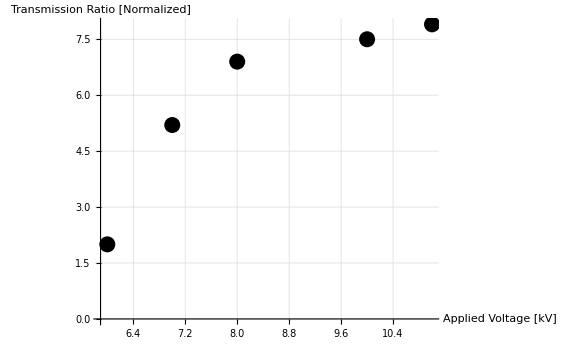

```mathematica
plot=ListPlot[Thread[{v,g}],AxesLabel->{Style["Applied Voltage\n[kV]",Black,18,Bold],Style["Transmission Ratio\n[Normalized]",Black,18,Bold]}
,TicksStyle->Directive["Label", 18,Black,Bold,FontFamily->"Arial"]
,PlotStyle->{PointSize[0.02],Black}
,GridLines->Automatic
,ImageSize->Large]
```

```mathematica
Export["voltage vs guiding.png",plot]
Export["voltage vs guiding.pdf",plot]
```

voltage vs guiding.png

voltage vs guiding.pdf